```mathematica
df[f_,r_]:=f''[r]-l1(2r f'[r]+(r^2-l2)f[r])/(r^2(r^2-l1))+f[r];
fs[z0_,s_]:=Function[z,(z-z0)^s Sum[b[n](z-z0)^n,{n, 0, ∞}]];
```

```mathematica
tmp=df[(r^2(r^2-l1)fs[√l1,0][#]&),r]//FullSimplify
```

(-l1 r^2+r^4) ∑_(n=0)^∞ (-1+n) n (-√l1+r)^(-2+n) b[n]-2 l1 r ∑_(n=0)^∞ n (-√l1+r)^(-1+n) b[n]+(l1 l2-2 l1 r^2+r^4) ∑_(n=0)^∞ (-√l1+r)^n b[n]

```mathematica
Series[tmp,{r,√l1,4}]//Normal
```

(2 l1^(3/2) (-√l1+r)+5 l1 (-√l1+r)^2+4 √l1 (-√l1+r)^3+(-√l1+r)^4) ∑_(n=0)^∞ (-1+n) n (-√l1+r)^(-2+n) b[n]+(-2 l1^(3/2)-2 l1 (-√l1+r)) ∑_(n=0)^∞ n (-√l1+r)^(-1+n) b[n]+(-l1^2+l1 l2+4 l1 (-√l1+r)^2+4 √l1 (-√l1+r)^3+(-√l1+r)^4) ∑_(n=0)^∞ (-√l1+r)^n b[n]

Допуская, что умножение рядов возможно, внесем (r-√l1) в суммы.

```mathematica
(2 l1^(3/2) ∑_(n=0)^∞ (-1+n) n (-√l1+r)^(-1+n) b[n]+5 l1 ∑_(n=0)^∞ (-1+n) n (-√l1+r)^n b[n]+4 √l1 ∑_(n=0)^∞ (-1+n) n (-√l1+r)^(+1+n) b[n]+∑_(n=0)^∞ (-1+n) n (-√l1+r)^(+2+n) b[n]) +(-2 l1^(3/2)∑_(n=0)^∞ n (-√l1+r)^(-1+n) b[n]-2 l1 ∑_(n=0)^∞ n (-√l1+r)^n b[n]) +((-l1^2+l1 l2)∑_(n=0)^∞ (-√l1+r)^n b[n]+4 l1 ∑_(n=0)^∞ (-√l1+r)^(+2+n) b[n]+4 √l1 ∑_(n=0)^∞ (-√l1+r)^(+3+n) b[n]+∑_(n=0)^∞ (-√l1+r)^(+4+n) b[n]) ;
```

Поменяем индексы в суммах, чтобы внутри остались только члены вида (r-√l1)^n.

```mathematica
(2 l1^(3/2) ∑_(n=-1)^∞ (1+n) n (-√l1+r)^n b[n+1]+5 l1 ∑_(n=0)^∞ (-1+n) n (-√l1+r)^n b[n]+4 √l1 ∑_(n=1)^∞ (-2+n) (n-1) (-√l1+r)^n b[n-1]+∑_(n=2)^∞ (-3+n) (n-2) (-√l1+r)^n b[n-2]) +(-2 l1^(3/2)∑_(n=-1)^∞ (n+1) (-√l1+r)^n b[n+1]-2 l1 ∑_(n=0)^∞ n (-√l1+r)^n b[n]) +((-l1^2+l1 l2)∑_(n=0)^∞ (-√l1+r)^n b[n]+4 l1 ∑_(n=2)^∞ (-√l1+r)^n b[n-2]+4 √l1 ∑_(n=3)^∞ (-√l1+r)^n b[n-3]+∑_(n=4)^∞ (-√l1+r)^n b[n-4]) ;
```

Рассмотрим член перед (r-l1)^n. Это выражение справедливо для n >= 4.

```mathematica
((2 l1^(3/2) (1+n) n (-√l1+r)^n b[n+1]+5 l1 (-1+n) n (-√l1+r)^n b[n]+4 √l1 (-2+n) (n-1) (-√l1+r)^n b[n-1]+(-3+n) (n-2) (-√l1+r)^n b[n-2]) +(-2 l1^(3/2)(n+1) (-√l1+r)^n b[n+1]-2 l1 n (-√l1+r)^n b[n]) +((-l1^2+l1 l2)(-√l1+r)^n b[n]+4 l1 (-√l1+r)^n b[n-2]+4 √l1 (-√l1+r)^n b[n-3]+(-√l1+r)^n b[n-4]))/(-√l1+r)^n  //FullSimplify
```

b[-4+n]+4 √l1 b[-3+n]+(6+4 l1-5 n+n^2) b[-2+n]+√l1 (4 (-2+n) (-1+n) b[-1+n]+√l1 (-l1+l2+n (-7+5 n)) b[n]+2 l1 (-1+n^2) b[1+n])

Отсюда можно получить решение для b[n+1] через b[n], b[n-1], b[n-2], b[n-3], b[n-4].

```mathematica
bs[n+1]=(b[1+n]/.First@Solve[%==0,b[1+n]]/.b->bs//FullSimplify)
```

1/(2 l1^(3/2) (-1+n^2))(-bs[-4+n]-4 √l1 bs[-3+n]-(6+4 l1-5 n+n^2) bs[-2+n]-4 √l1 (-2+n) (-1+n) bs[-1+n]+l1 (l1-l2+(7-5 n) n) bs[n])

Однако для n < 4 подход должен быть другим.

```mathematica
tmpser=Series[tmp/.∞->9//FullSimplify,{r,√l1,10}]
```

(-l1^2 b[0]+l1 l2 b[0]-2 l1^(3/2) b[1])+(-2 l1 b[1]-l1^2 b[1]+l1 l2 b[1]) (r-√l1)+(4 l1 b[0]+6 l1 b[2]-l1^2 b[2]+l1 l2 b[2]+6 l1^(3/2) b[3]) (r-√l1)^2+(4 √l1 b[0]+4 l1 b[1]+8 √l1 b[2]+24 l1 b[3]-l1^2 b[3]+l1 l2 b[3]+16 l1^(3/2) b[4]) (r-√l1)^3+(b[0]+4 √l1 b[1]+2 b[2]+4 l1 b[2]+24 √l1 b[3]+52 l1 b[4]-l1^2 b[4]+l1 l2 b[4]+30 l1^(3/2) b[5]) (r-√l1)^4+(b[1]+4 √l1 b[2]+6 b[3]+4 l1 b[3]+48 √l1 b[4]+90 l1 b[5]-l1^2 b[5]+l1 l2 b[5]+48 l1^(3/2) b[6]) (r-√l1)^5+(b[2]+4 √l1 b[3]+12 b[4]+4 l1 b[4]+80 √l1 b[5]+138 l1 b[6]-l1^2 b[6]+l1 l2 b[6]+70 l1^(3/2) b[7]) (r-√l1)^6+(b[3]+4 √l1 b[4]+20 b[5]+4 l1 b[5]+120 √l1 b[6]+196 l1 b[7]-l1^2 b[7]+l1 l2 b[7]+96 l1^(3/2) b[8]) (r-√l1)^7+(b[4]+4 √l1 b[5]+30 b[6]+4 l1 b[6]+168 √l1 b[7]+264 l1 b[8]-l1^2 b[8]+l1 l2 b[8]+126 l1^(3/2) b[9]) (r-√l1)^8+(b[5]+4 √l1 b[6]+42 b[7]+4 l1 b[7]+224 √l1 b[8]+342 l1 b[9]-l1^2 b[9]+l1 l2 b[9]) (r-√l1)^9+(b[6]+4 √l1 b[7]+56 b[8]+4 l1 b[8]+288 √l1 b[9]) (r-√l1)^10+O[r-√l1]^11

Найдем выражения для первых нескольких коэффициентов.

```mathematica
SeriesCoefficient[tmpser,0]
bs1[1]=b[1]/.First@Solve[SeriesCoefficient[tmpser,0]==0,b[1]]/.b->bs//FullSimplify
bs1[1]/.{l1->(l-1)(l+2),l2->l(l+1)}//FullSimplify
```

-l1^2 b[0]+l1 l2 b[0]-2 l1^(3/2) b[1]

((-l1+l2) bs[0])/(2 √l1)

bs[0]/(√(-2+l+l^2))

```mathematica
SeriesCoefficient[tmpser,1]
bs2[1]=b[1]/.First@Solve[SeriesCoefficient[tmpser,1]==0,b[1]]/.b->bs//FullSimplify
bs2[1]/.{l1->(l-1)(l+2),l2->l(l+1)}//FullSimplify
```

-2 l1 b[1]-l1^2 b[1]+l1 l2 b[1]

0

0

```mathematica
bs[1]=bs1[1];
```

```mathematica
SeriesCoefficient[tmpser,2]
bs[3]=b[3]/.First@Solve[SeriesCoefficient[tmpser,2]==0,b[3]]/.b->bs//FullSimplify
bs[3]/.{l1->(l-1)(l+2),l2->l(l+1)}//FullSimplify
```

4 l1 b[0]+6 l1 b[2]-l1^2 b[2]+l1 l2 b[2]+6 l1^(3/2) b[3]

(-4 bs[0]+(-6+l1-l2) bs[2])/(6 √l1)

-(2 (bs[0]+2 bs[2]))/(3 √(-2+l+l^2))

```mathematica
SeriesCoefficient[tmpser,3]
bs[4]=b[4]/.First@Solve[SeriesCoefficient[tmpser,3]==0,b[4]]/.b->bs//FullSimplify
bs[4]/.{l1->(l-1)(l+2),l2->l(l+1)}//FullSimplify
```

4 √l1 b[0]+4 l1 b[1]+8 √l1 b[2]+24 l1 b[3]-l1^2 b[3]+l1 l2 b[3]+16 l1^(3/2) b[4]

(8 (9+l1-l2) bs[0]+(96+l1^2-2 l1 (15+l2)+l2 (30+l2)) bs[2])/(96 l1)

(7 bs[0]+20 bs[2])/(12 (-2+l+l^2))

```mathematica
SeriesCoefficient[tmpser,4]
bs[5]=b[5]/.First@Solve[SeriesCoefficient[tmpser,4]==0,b[5]]/.b->bs//FullSimplify
bs[5]/.{l1->(l-1)(l+2),l2->l(l+1)}//FullSimplify
```

b[0]+4 √l1 b[1]+2 b[2]+4 l1 b[2]+24 √l1 b[3]+52 l1 b[4]-l1^2 b[4]+l1 l2 b[4]+30 l1^(3/2) b[5]

1/(2880 l1^(3/2))(8 (-288+l1^2+l2 (19+l2)-l1 (19+2 l2)) bs[0]+(-2880+l1^3-l1^2 (82+3 l2)-l2 (1272+l2 (82+l2))+l1 (888+l2 (164+3 l2))) bs[2])

(-41 bs[0]-8 (13+l+l^2) bs[2])/(60 (-2+l+l^2)^(3/2))

b[0] и b[2] являются параметрами.

```mathematica
bs[0]=α;
bs[1]=bs[1]/.{l1->(l-1)(l+2),l2->l(l+1)}//FullSimplify;
bs[2]=β;
bs[3]=bs[3]/.{l1->(l-1)(l+2),l2->l(l+1)}//FullSimplify;
bs[4]=bs[4]/.{l1->(l-1)(l+2),l2->l(l+1)}//FullSimplify;
bs[5]=bs[5]/.{l1->(l-1)(l+2),l2->l(l+1)}//FullSimplify;
{ bs[0], bs[1], bs[2], bs[3], bs[4], bs[5] }//FullSimplify
bs[n]=bs[n+1]/.{l1->(l-1)(l+2),l2->l(l+1),n->(n-1)}//FullSimplify
```

{α,α/(√(-2+l+l^2)),β,-(2 (α+2 β))/(3 √(-2+l+l^2)),(7 α+20 β)/(12 (-2+l+l^2)),(-41 α-8 (13+l+l^2) β)/(60 (-2+l+l^2)^(3/2))}

1/(2 (-2+l+l^2)^(3/2) (-2+n) n)(-bs[-5+n]-4 √(-2+l+l^2) bs[-4+n]-(4+4 l (1+l)+(-7+n) n) bs[-3+n]-4 √(-2+l+l^2) (-3+n) (-2+n) bs[-2+n]-(-1+l) (2+l) (-2+n) (-7+5 n) bs[-1+n])

Получим несколько более высоких коэффициентов.

```mathematica
(bs[n]/.{n->5})//FullSimplify
```

(-41 α-8 (13+l+l^2) β)/(60 (-2+l+l^2)^(3/2))

```mathematica
(bs[n]/.{n->6})//FullSimplify
```

(2 (61+5 l (1+l)) α+318 β+51 l (1+l) β)/(180 (-2+l+l^2)^2)

```mathematica
(bs[n]/.{n->7})/.{bs[6]->(bs[n]/.{n->6})}//FullSimplify
```

(-(431+67 l (1+l)) α-6 (186+47 l (1+l)) β)/(630 (-2+l+l^2)^(5/2))

Изобразим функцию для получения серии коэффициентов.

```mathematica
coeflist[len_]:=Module[{coefs},
coefs[0]=bs[0];coefs[1]=bs[1];coefs[2]=bs[2];
coefs[3]=bs[3];coefs[4]=bs[4];
Do[coefs[i]=((bs[n]/.n->i)/.Table[bs[j]->coefs[j],{j,i-5,i-1}])//Simplify,{i,5,len}];
Return[Array[coefs,len,{0,len-1}]];
];
```

```mathematica
coeflist[11]
```

{α,α/(√(-2+l+l^2)),β,-(2 (α+2 β))/(3 √(-2+l+l^2)),(7 α+20 β)/(12 (-2+l+l^2)),(-41 α-8 (13+l+l^2) β)/(60 (-2+l+l^2)^(3/2)),(2 (61+5 l+5 l^2) α+3 (106+17 l+17 l^2) β)/(180 (-2+l+l^2)^2),(-(431+67 l+67 l^2) α-6 (186+47 l+47 l^2) β)/(630 (-2+l+l^2)^(5/2)),(3 (2298+541 l+541 l^2) α+8 (2234+759 l+766 l^2+14 l^3+7 l^4) β)/(10080 (-2+l+l^2)^3),(-(62066+19257 l+19417 l^2+320 l^3+160 l^4) α-8 (20108+8472 l+8659 l^2+374 l^3+187 l^4) β)/(90720 (-2+l+l^2)^(7/2)),(4 (77582+29571 l+30145 l^2+1148 l^3+574 l^4) α+5 (160868+79968 l+82927 l^2+5918 l^3+2959 l^4) β)/(453600 (-2+l+l^2)^4)}

Изобразим функцию, представляемую рядом с этими коэффициентами.

```mathematica
fs2[coefs_,l0_,a_,b_]:=Function[r,Sum[N@(coefs[[n+1]]/.{l->l0,α->a,β->b})(r-N@√((l0-1)(l0+2)))^n,{n,0,Length[coefs]-1}]];
```

```mathematica
plotfs2[n_,l_,a_,b_]:=Module[{coefs},coefs=coeflist[n]//N;Plot[fs2[coefs,l,a,b][r],{r,0.5 √((l-1)(l+2)),2 √((l-1)(l+2))}]];
```

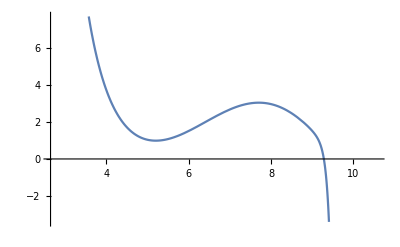

```mathematica
plotfs2[50,5,1,1]
```